## Этап второй

### Расчет кинематических и динамических параметров движения жидкости в гидростаки

Отметки уровней расположения свободных поверхностей и элементов:

ΔB=0м, ΔП=1.4 м, ΔХл=1.7м, ΔН=0.5м, ΔТ=3м

Размеры труб:

l_вс=2.4м, d_вс=30мм, Δ_вс=0.1мм
l_н=13м, d_н=33мм, Δ_н=0.1мм
l_вс=3.3м
l_вс=3.5м, d_вс=6мм

Коэффициенты сопротивления вентилей - ζ_н=ζ_хл=3.3;

Коэффициент сопротивления приемного клапана с сеткой ζ_к=6.5;

Плотность воды ρ=10^3 кг/м^3

Кинематический коэффициент вязкости воды ν=10^-6 м^2/с

1. Определить графическим методом расход Q воды во всасывающей трубе насоса, если вакуум на входе в насос p_в=30 кПа.

Примечание: считать, что резиновый рукав хлоратора присоединяется к всасывающему трубопроводу непосредственно у входа в насос.

2. Вычислить величину вакуума p_вхл в хлораторе, необходимого для самотечного движения раствора хлора из хлоратора на вход в насос в количестве q=0.005 л/с.

3. Подобрать диаметр d_п резинового рукава по которому раствор хлора поступает из питателя в хлоратор, необходимый для поддержания значения вакуума p_вхл в хлораторе неизменным.

Примечание: учитывать только потери на трение по длине.

Коэффициент потерь на трение λ для резиновых рукавов определить:

- при ламинарном режиме движения жидкости по имперической формуле, учитывающей искажение геометрии поперечного сечения по длине рукава, а также некоторое охлаждение слоев жидкости, прилегающих к его внутренней поверхности:

λ=108/Re

- при турбулентном по формуле:

λ=0.316/Re^0.25

Критическое число Рейнольдса для резиновых рукавов ориентировочно принять равным - Re_кр=1600.

-Graphics-

1. Будем определять коэффициент потерь на трение λ во всасывающей трубе будем определять по формулам:

-Graphics-

Запишем кусочно-заданную функцию для λ:

```mathematica
λ[Δ_,d_,re_]:=Piecewise[{{64/re,re<2300},{0.3164/re^0.25,4000<re<10 d/Δ },{0.11(Δ/d+68/re)^0.25,10 d/Δ<re≤ 560d/Δ },{1/(-2Log10[Δ/(3.71d)])^2,re≥ 560d/Δ}}]
```

А также функцию числа Рейнольдса:

```mathematica
re[Q_]:=4 Q/(π d ν)
```

Построим зависимость для λ при Δ_вс=0,1мм, d_вс=30мм:

```mathematica
ListPlot[ParallelTable[{re,λ[0.01 10^-3,30 10^-3,re]},{re,1000, 10 10^5,100}],PlotRange->All,AxesLabel->{Re,λ},PlotLabels->{300}]
```

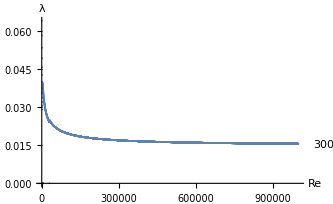

Запишем уравнение Бернули для всасывающей трубы, сечение 1-1 на поверхности водоема, 2-2 у входа в насос:

ΔB=ΔH+p_2/(ρ g)+0.0827 Q^2/d_вс^4+∑_1^2 h_п,

где p_2=p_в-p_ат, ∑_1^2 h_п=(ζ_к+λ l_вс/d_вс)0.0827 Q^2/d_вс^4

Отсюда получим:

ΔB-ΔH-p_2/(ρ g)=0.0827 Q^2/d_вс^4(1+ζ_к+λ l_вс/d_вс)

Где левая часть - постоянная, правая - переменная. Решим задачу графически:

```mathematica
Show[Plot[ΔB-ΔH-p2/(ρ g),{Q,0,4 10^-3},PlotLabels->{"левая часть"}],ListLinePlot[Table[{Q,0.0827 Q^2/d^4(1+ζ+λ[Δ,d,re[Q]] l/d)},{Q,10^-4,4 10^-3,1 10^-4}],PlotLabels->{"правая часть"}]]
```

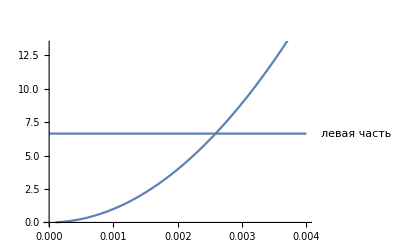

Получили ответ Q=2.59 л/с

2. Для того чтобы опредить величину вакуума в хлораторе, составим уравнение баланса напоров для сечений 3-3 и 4-4:

ΔХл+p_3/(ρ g)=ΔH+p_4/(ρ g)+0.0827 q^2/d_хл^4+∑_3^4 h_п,
p_4=p_2=p_в-p_ат, ∑_3^4 h_п=(ζ_хл+λ_рез l_хл/d_хл)0.0827 q^2/d_хл^4

Отсюда:

p_3=ρ g(ΔH-ΔХл+p_4/(ρ g)+(1+ζ_хл+λ_рез l_хл/d_хл)0.0827 q^2/d_хл^4)
p_3=-77кПа
p_вхл=p_ат+p_3=23кПа

3. Размер резинового рукава d_п найдем из уравнения Бернули для сечений 5-5 и 3-3:

ΔП=ΔХл+p_3/(ρ g)+∑_5^3 h_п,
 ∑_5^3 h_п=λ_рез l_п/d_п 0.0827 q^2/d_п^4

Находим:

d_п=((λ_рез l_п 0.0827 q^2)/(ΔП-ΔХл-p_3/(ρ g)))^(1/5)

d_п=0.0034м=3.4мм